# Vaja 4

1. naloga

```mathematica
trikotnik = Trikotnik[{0,0},{5,1},{7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[Trikotnik[A_,B_,C_]]:={
Daljica[A,B],Daljica[B,C],Daljica[A,C]
}
```

```mathematica
Stranice[trikotnik]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{0,0},{7,4}]}

```mathematica
Koti[Trikotnik[A_,B_,C_]] :={
Kot[C,A,B],Kot[A,B,C],Kot[B,C,A]
}
```

```mathematica
Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
Graphics[{Point[{0,0}],Point[{5,1}],Point[{7,4}]}]
```

-Graphics-

```mathematica
SlikaOgljisc[Trikotnik[A_,B_,C_]] :={
Point[A],Point[B],Point[C]
}
```

```mathematica
Graphics[SlikaOgljisc[trikotnik]]
```

-Graphics-

```mathematica
SlikaStranic[Trikotnik[A_,B_,C_]] :={
Line[{A,B}],Line[{B,C}],Line[{C,A}]
}
```

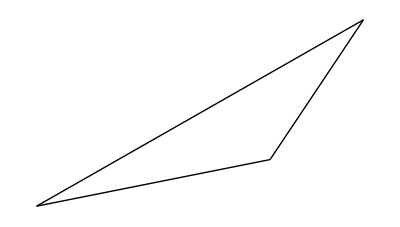

```mathematica
Graphics[SlikaStranic[trikotnik]]
```

```mathematica
NarisiTrikotnik[trikotnik_] :=Graphics[{SlikaOgljisc[trikotnik],SlikaStranic[trikotnik]}]
```

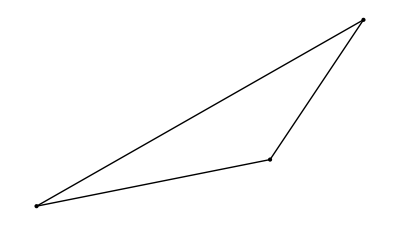

```mathematica
NarisiTrikotnik[trikotnik]
```

2. naloga

```mathematica
Dolzina[Daljica[A_,B_]] := Norm[A - B]
```

```mathematica
Dolzina[Daljica[{0,0},{1,1}]]
```

√2

```mathematica
VelikostKota[Kot[A_,B_,C_]]:=ArcCos[((A-B).(C - B))/(Norm[A-B]*Norm[C - B])]
```

```mathematica
VelikostKota[Kot[{0,1},{0,0},{1,0}]]
```

π/2

```mathematica
VektorSimetraleKota[Kot[A_,B_,C_],dol_:1]:=dol*Normalize[Normalize[(A -B)] + Normalize[(C - B)]]
```

```mathematica
VektorSimetraleKota[Kot[{7,4},{0,0},{5,1}]]
```

{(5/(√26)+7/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2)),(1/(√26)+4/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))}

```mathematica
PresecisceSimetraleKota[Kot[A_,B_,C_]] :=Module[{resitev,t},
resitev  = Solve[k *VektorSimetraleKota[Kot[A,B,C]]+B ==t *(A -C)+C,{k,t}]//First;
t = t /.resitev;
t*(A -C)+C
]
```

```mathematica
PresecisceSimetraleKota[Kot[{7,4},{0,0},{5,1}]]
```

{5+(4 √5)/(5 √2+2 √5),1+(6 √5)/(5 √2+2 √5)}

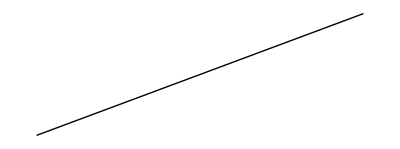

```mathematica
SlikaSimetrale[Kot[A_,B_,C_]] := Line[{B, PresecisceSimetraleKota[Kot[A,B,C]]}]
```

```mathematica
SlikaSimetralKotov[trikotnik_Trikotnik] := Map[SlikaSimetrale,Koti[trikotnik]]
```

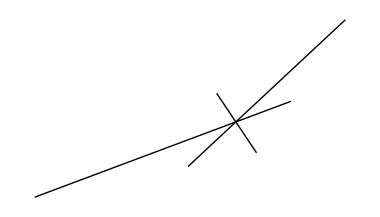

```mathematica
SlikaSimetralKotov[trikotnik]//Graphics
```

```mathematica
PresecisceSimetral[trikotnik_Trikotnik]:=Module[{ presecisce1, presecisce2,t},
presecisce1=PresecisceSimetraleKota[Koti[trikotnik][[1]]];
presecisce2=PresecisceSimetraleKota[Koti[trikotnik][[2]]];
resitev  = Solve[k *(presecisce1 - trikotnik[[1]])+trikotnik[[1]] ==t *(presecisce2 - trikotnik[[2]])+trikotnik[[2]],{k,t}]//First;
t = t/.resitev;
t *(presecisce2 - trikotnik[[2]])+trikotnik[[2]]
]
```

```mathematica
PresecisceSimetral[trikotnik]//N
```

{4.53302,1.6973}

```mathematica
NarisiTrikotnikSSimetralami[trikotnik_Trikotnik] := Graphics[{SlikaStranic[trikotnik],SlikaOgljisc[trikotnik],SlikaSimetralKotov[trikotnik],Point[{PresecisceSimetral[trikotnik]}]}]
```

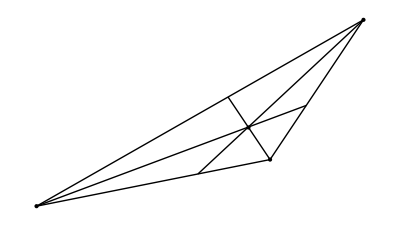

```mathematica
NarisiTrikotnikSSimetralami[trikotnik]
```

3. naloga

```mathematica
NajblizjaTockaNaPremici[{A_,B_},x_,y_]:=((B-A).({x,y}-A))/Norm[(B-A)]*(A-B)
```

```mathematica
NajblizjaTockaNaPremici[{{1,0},{2,0}},3,4]
```

```mathematica
{-2,0} dokoncaj
```